```mathematica
kmax=11;
weight=2/Sqrt[Pi]*Sqrt[x]*Exp[-x];
xmin = 0;
xmax = Infinity;
p=Array[0&,{kmax, 1}];p[[1]]=1;
np=Array[0&,{kmax, 1}];
an=Array[0&,{kmax, 1}];
mp=Array[0&,{kmax, 1}];
bn=Array[0&,{kmax, 1}];
For[k=1,k<=kmax,k=k+1,
If[k==2,p[[k]]=Simplify[(x-an[[k-1]])*p[[k-1]]]];
If[k>2,p[[k]]=Simplify[(x-an[[k-1]])*p[[k-1]]-bn[[k-1]]*p[[k-2]]]];
np[[k]]=NIntegrate[p[[k]]^2*weight,{x,xmin,xmax},WorkingPrecision->100,PrecisionGoal->90];
mp[[k]]=NIntegrate[x*p[[k]]^2*weight,{x,xmin,xmax},WorkingPrecision->100,PrecisionGoal->90];
an[[k]]=mp[[k]]/np[[k]];
If[k==1,bn[[k]]=np[[k]],bn[[k]]=np[[k]]/np[[k-1]]];
]
```

NIntegrate::precw: The precision of the argument function ((2 ⅇ^-x √x (3.75-5. x+x^2)^2)/(√π)) is less than WorkingPrecision (100.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {83.7198894703969355100666957319790768677769346315861400983530391762540966143226474112360097279143363672099724525346151459711795529898200374359566008871}. NIntegrate obtained 7.50000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000025212134408766667031551783363260006174191732 and 1.21048768635308371076484775054166522366267827526631944458077146492746509716643190954996627921446358556674830335990644110561061925508163823720497025934×10^-70 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function ((2 ⅇ^-x x^(3/2) (3.75-5. x+x^2)^2)/(√π)) is less than WorkingPrecision (100.).

NIntegrate::precw: The precision of the argument function ((2 ⅇ^-x √x (-«136»+«135» x-«135» x^2+x^3)^2)/(√π)) is less than WorkingPrecision (100.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

```mathematica
For[k=1,k<=kmax,k=k+1,
p[[k]]=Simplify[p[[k]]/Sqrt[np[[k]]]];
]
```

```mathematica
nodes=Array[0&,kmax*(kmax+1)/2];
gaussweights = Array[0&,kmax*(kmax+1)/2];
```

```mathematica
For[k=2,k≤kmax,k=k+1,J=DiagonalMatrix[an[[1;;k]]]+DiagonalMatrix[Sqrt[bn[[2;;k]]],1]+DiagonalMatrix[Sqrt[bn[[2;;k]]],-1];
nodes[[k*(k-1)/2+1;;k*(k-1)/2+k]]=Eigenvalues[N[J,32]];
For[i=1,i≤k,i=i+1,
pi=Evaluate[Table[HornerForm[N[p[[l]],32]],{l,1,k}]/.x->nodes[[k*(k-1)/2+i]]];
gaussweights[[k*(k-1)/2+i]]=1/(pi.pi);
]
]
```

```mathematica
ScientificForm[Grid[Transpose[{Flatten[CoefficientList[p,x]], nodes,gaussweights}]],17,NumberFormat->(Row[{#1,"e",If[#3≠"",#3,"0"]}]&)]
```

1.0000000000000000e0 | 0e0 | 0e0
-1.2247448713915890e0 | 4.0811388300841897e0 | 1.8377223398316207e-1
8.1649658092772603e-1 | 9.1886116991581033e-1 | 8.1622776601683793e-1
1.3693063937629153e0 | 7.0328990381473726e0 | 1.5423678039252684e-2
-1.8257418583505537e0 | 2.8007750541502566e0 | 3.4457514218329290e-1
3.6514837167011074e-1 | 6.6632590770237082e-1 | 6.4000117977745442e-1
-1.4790199457749040e0 | 1.0182437613815925e1 | 9.1014065014776803e-4
2.9580398915498080e0 | 5.1373875461767116e0 | 5.7315599552891789e-2
-1.1832159566199232e0 | 2.1566487632690943e0 | 4.3060862766817673e-1
1.1268723396380221e-1 | 5.2352607673826911e-1 | 5.1116563212878372e-1
1.5687375497513917e0 | 1.3457678352057580e1 | 4.3720496840175460e-5
-4.1833001326703777e0 | 7.7467037795425571e0 | 6.0632499271298957e-3
2.5099800796022266e0 | 4.1044653628283150e0 | 1.1033271191035714e-1
-4.7809144373375746e-1 | 1.7597536984236964e0 | 4.6555161203059889e-1
2.6560635762986525e-2 | 4.3139880714785148e-1 | 4.1800870563507390e-1
-1.6453058226360229e0 | 1.6820970077828382e1 | 1.8318895245082608e-6
5.4843527421200763e0 | 1.0540469858448344e1 | 4.8598297306743220e-4
-4.3874821936960610e0 | 6.3490679256803796e0 | 1.7300863449618992e-2
1.2535663410560174e0 | 3.4340079684240713e0 | 1.6168079428163909e-1
-1.3928514900622416e-1 | 1.4885342923104525e0 | 4.7138282273876961e-1
5.0649145093172422e-3 | 3.6694987730837072e-1 | 3.4914770466738037e-1
1.7124885948525321e0 | 2.0249916365870878e1 | 6.9575876831873967e-8
-6.8499543794101286e0 | 1.3468535743251481e1 | 3.2192060974207623e-5
6.8499543794101286e0 | 8.8040795780567753e0 | 1.9869562376932428e-3
-2.6095064302514776e0 | 5.4090315972444334e0 | 3.3911545043519469e-2
4.3491773837524626e-1 | 2.9583744586966498e0 | 2.0549785485210272e-1
-3.1630380972745183e-2 | 1.2907586229591527e0 | 4.6166716183338569e-1
8.1103540955756878e-4 | 3.1930363392063005e-1 | 2.9690422039644784e-1
-1.7725941001114722e0 | 2.3730003995934708e1 | 2.4530321345408097e-9
8.2721058005202037e0 | 1.6499410797655816e1 | 1.8532244582470076e-6
-9.9265269606242444e0 | 1.1417182076545830e1 | 1.8325396748959754e-4
4.7269176002972593e0 | 7.6052562992316137e0 | 5.1256820846894768e-3
-1.0504261333993909e0 | 4.7241145375277907e0 | 5.4023954619386445e-2
1.1459194182538810e-1 | 2.6015248434060294e0 | 2.4024204721432566e-1
-5.8765098371993899e-3 | 1.1398738015816137e0 | 4.4412388238208243e-1
1.1193352070855981e-4 | 2.8263364811659913e-1 | 2.5629932405453601e-1
1.8271481765265714e0 | 2.7251236523027062e1 | 8.1566548665890901e-11
-9.7447902748083809e0 | 1.9611902819165948e1 | 9.5735177932379712e-8
1.3642706384731733e1 | 1.4154053671278046e1 | 1.4336471296691242e-5
-7.7958322198467047e0 | 9.9720091595393480e0 | 6.1232707227744695e-4
2.1655089499574180e0 | 6.7139743166150287e0 | 1.0165013765568040e-2
-3.1498311999380625e-1 | 4.1993506006572931e0 | 7.5709847078868682e-2
2.4229470768754327e-2 | 2.3230960770224661e0 | 2.6638190989313319e-1
-9.2302745785730770e-4 | 1.0208442777203897e0 | 4.2305280272502488e-1
1.3573933203783937e-5 | 2.5353255497441909e-1 | 2.2406366717708659e-1
-1.8772163008132714e0 | 3.0806405917052723e1 | 2.5864950210507910e-12
1.1263297804879628e1 | 2.2791002894948946e1 | 4.5357456103990524e-9
-1.8021276487807405e1 | 1.6990847293542554e1 | 9.8591857437905302e-7
1.2014184325204937e1 | 1.2474832404836205e1 | 6.1144384869619967e-5
-4.0047281084016456e0 | 8.8803475979967086e0 | 1.4987308444561214e-3
7.2813238334575374e-1 | 6.0199180277014609e0 | 1.7049558753974314e-2
-7.4680244445718332e-2 | 3.7828808737072902e0 | 9.7442427232973978e-2
4.2674425397553333e-3 | 2.0994104627087982e0 | 2.8512286460557075e-1
-1.2551301587515686e-4 | 9.2448154698665736e-1 | 4.0082667158932749e-1
1.4679884897679165e-6 | 2.2987298051865622e-1 | 1.9799761213192125e-1
1.9235743011490395e0 | 3.4390125899880688e1 | 7.8854951538827899e-14
-1.2823828674326930e1 | 2.6025655381891422e1 | 2.0018260696213391e-10
2.3082891613788474e1 | 1.9910257642768470e1 | 6.1091749439769798e-8
-1.7586965039076932e1 | 1.5089128220021153e1 | 5.2963217183076198e-6
6.8393752929743626e0 | 1.1189875716176443e1 | 1.8306534821380725e-4
-1.4922273366489518e0 | 8.0191126887820446e0 | 2.9962030812517749e-3
1.9131119700627588e-1 | 5.4616447726944182e0 | 2.5508691377753915e-2
-1.4576091200478162e-2 | 3.4435372681407951e0 | 1.1817776915869690e-1
6.4306284707991891e-4 | 1.9155655747361731e0 | 2.9781055635734131e-1
-1.5042405779647226e-5 | 8.4483941642521249e-1 | 3.7873604461919106e-1
1.4326100742521168e-7 | 2.1025741848317982e-1 | 1.7658231244382202e-1

```mathematica
testpoly=x^5;q=10;
Integrate[testpoly*x^2*Exp[-x^2]*4/Sqrt[Pi],{x,xmin,xmax}]-(testpoly/.x->nodes[[q*(q-1)/2+1;;q*(q-1)/2+q]]).gaussweights[[q*(q-1)/2+1;;q*(q-1)/2+q]]
```

-318.073474997426924556623047

```mathematica
testf=(1.2+Cos[2*y+1.75])*Exp[-y^2]
```

ⅇ^(-y^2) (1.2+Cos[1.75+2 y])

```mathematica
coeffspr=NIntegrate[testf*(p/.x->y^2)*y^2,{y,0,Infinity},WorkingPrecision->100,PrecisionGoal->90]
```

NIntegrate::precw: The precision of the argument function (1.062251932027196914477073048507513538754641312768661574904192765190444933263000525823677106543946703 ⅇ^(-y^2) y^2 (1.2+Cos[1.75+2 y])) is less than WorkingPrecision (100.).

NIntegrate::precw: The precision of the argument function (0.8673250705840775183190308265899921796160837168226672349313664898690237565740261522330057880061826469 ⅇ^(-y^2) y^2 (-1.5+y^2) (1.2+Cos[1.75+2 y])) is less than WorkingPrecision (100.).

NIntegrate::precw: The precision of the argument function (0.387879563283160111702819385489664916488585141469418538571753880228080285940993743162005057997140688 ⅇ^(-y^2) y^2 («134»-«135» y^2+y^4) (1.2+Cos[1.75+2 y])) is less than WorkingPrecision (100.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

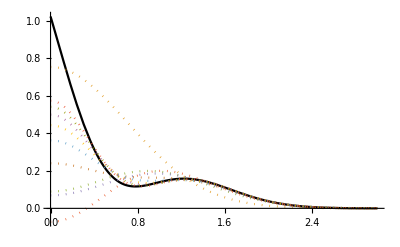

```mathematica
Plot[{testf,Evaluate[Table[2*Exp[-y^2]*coeffspr[[1;;k]].(p[[1;;k]]/.x->y^2),{k,1,kmax}]]},{y,0,3},PlotRange->All, PlotStyle->{Black,Dotted, Dotted, Dotted, Dotted, Dotted, Dotted, Dotted, Dotted, Dotted, Dotted}]
```

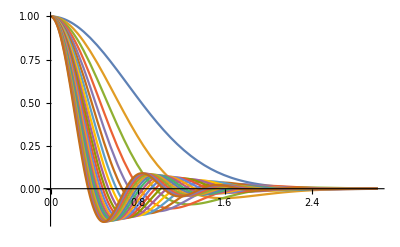

```mathematica
Plot[Evaluate[Table[Exp[-y^2]*HornerForm[N[p[[k]],32]/.x->y^2]/(p[[k]]/.x->0),{k,1,kmax}]],{y,0,3}, PlotRange->All]
```

```mathematica
Integrate[x^2*Exp[-x^2],{x,0,Infinity}]
```

(√π)/4